Module 1: Setting up Hamiltonian for the whole system without PBC
Basis states: |uu...u> , |uu...d>, |u....du>, |u....dd>, ... |dd...d>

```mathematica
Timing[
Clear["Global`*"];

n=12; (* No of sites *)
cut=6; (* Where the motif is *)

If[cut<n, 
(
dim=2^n; (* Dimension of Hilbert space *)
Print["Dim of Hilbert space: ",dim];

(* Spin matrices in the many-body Hilbert space *)
Do[
list1=Table[1,2^(n-i)];
If[i>1,list1=PadRight[list1,2^(n-i+1)]];
list2=Table[1,2^(n-i)];
list2=PadRight[list2,2^(n-i+1),-1];

S[i,1]=0.5*SparseArray[{Band[{1,1+2^(n-i)},{dim,dim}]->list1,Band[{1+2^(n-i),1},{dim,dim}]->list1}];
S[i,2]=0.5*SparseArray[{Band[{1,1+2^(n-i)},{dim,dim}]->-ⅈ*list1,Band[{1+2^(n-i),1},{dim,dim}]->ⅈ*list1}];
S[i,3]=0.5*SparseArray[{Band[{1,1},{dim,dim}]->list2}];
,{i,1,n}];

(* I put a Heisenberg model *)
HA[Ja_]:=-Ja*Sum[(S[i,1].S[i+1,1]+S[i,2].S[i+1,2]+S[i,3].S[i+1,3]),{i,1,cut-2}];
HB[Jb_]:=-Jb*Sum[(S[i,1].S[i+1,1]+S[i,2].S[i+1,2]+S[i,3].S[i+1,3]),{i,cut+2,n-1}];
HAB[Jab_]:=-Jab*((S[cut-1,1].S[cut,1]+S[cut-1,2].S[cut,2]+S[cut-1,3].S[cut,3])+
+(S[cut-1,1].S[cut+1,1]+S[cut-1,2].S[cut+1,2]+S[cut-1,3].S[cut+1,3])+2(S[cut,1].S[cut+1,1]+S[cut,2].S[cut+1,2]+S[cut,3].S[cut+1,3])+(S[cut,1].S[cut+2,1]+S[cut,2].S[cut+2,2]+S[cut,3].S[cut+2,3])+(S[cut+1,1].S[cut+2,1]+S[cut+1,2].S[cut+2,2]+S[cut+1,3].S[cut+2,3]));
);
];
Clear[list1,list2];
]
```

Dim of Hilbert space: 4096

{0.144477,Null}

Module 2: Check commutation relation: [HA, HAB], [HB,HAB], [HA,HB]
If Max-Min=0, then the commutator is zero

```mathematica
com1=HA[Ja].HAB[Jab]-HAB[Jab].HA[Ja];
com2=HB[Jb].HAB[Jab]-HAB[Jab].HB[Jb];
com3=HA[Ja].HB[Jb]-HB[Jb].HA[Ja];
Max[com1]-Min[com1]//Chop
Max[com2]-Min[com2]//Chop
Max[com3]-Min[com3]//Chop
```

Max[0,-0.5 Ja Jab,-0.25 Ja Jab,0.25 Ja Jab,0.5 Ja Jab]-Min[0,-0.5 Ja Jab,-0.25 Ja Jab,0.25 Ja Jab,0.5 Ja Jab]

Max[0,-0.5 Jab Jb,-0.25 Jab Jb,0.25 Jab Jb,0.5 Jab Jb]-Min[0,-0.5 Jab Jb,-0.25 Jab Jb,0.25 Jab Jb,0.5 Jab Jb]

0

Option 1: Setting up the Hamiltonian for the subsystem A and obtain eigenstates

```mathematica
Timing[
nA=cut-1;
dimA=2^nA; (* Dimension of Hilbert space for A *)

(* Spin matrices in the subsstem Hilbert space *)
Do[
l1=Table[1,2^(nA-i)];
If[i>1,l1=PadRight[l1,2^(nA-i+1)]];

l2=Table[1,2^(nA-i)];
l2=PadRight[l2,2^(nA-i+1),-1];

s[i,1]=0.5*SparseArray[{Band[{1,1+2^(nA-i)},{dimA,dimA}]->l1,Band[{1+2^(nA-i),1},{dimA,dimA}]->l1}];
s[i,2]=0.5*SparseArray[{Band[{1,1+2^(nA-i)},{dimA,dimA}]->-ⅈ*l1,Band[{1+2^(nA-i),1},{dimA,dimA}]->ⅈ*l1}];
s[i,3]=0.5*SparseArray[{Band[{1,1},{dimA,dimA}]->l2}];
,{i,1,nA}];

(* Copy from HA, but need to change the dimension *)
Haaa[Ja_]:=-Ja*Sum[s[i,1].s[i+1,1]+s[i,2].s[i+1,2]+s[i,3].s[i+1,3],{i,1,nA-1}]//N;
Clear[l1,l2];
];
```

Option 2: Put a random state for subsystem A (or B as well)

```mathematica
(* General a random complex vector with norm 1 *)
sphericalrandomcomplex[n_]:=Normalize/@(RandomVariate[NormalDistribution[0,1],{1,2^n,2}].{1,I});
ranA=Flatten[sphericalrandomcomplex[nA]];
ranB=Flatten[sphericalrandomcomplex[nA]];
ranbond=Flatten[sphericalrandomcomplex[2]];
ran=Flatten[sphericalrandomcomplex[n]];

(* Check normalization *)
Norm[ranA]
Norm[ranB]
Norm[ran]
Norm[ranbond]
```

1.

1.

1.

«1 more identical outputs»

Module 3: Diagonalize the time-independent Hamiltonian and simulate the dynamics

```mathematica
Timing[
(* Hamiltonian *)
H[Ja_,Jb_,Jab_]:=Normal[HA[Ja]+HB[Jb]+HAB[Jab]];

(* Parameters *)
Ja=1.;
Jb=1.;
Jab=1.;
shift=50.; (* To sort the spectrum correctly *)

(* Diagonalize the Hamiltonian for the whole system AxB *)
sol=Eigensystem[H[Ja,Jb,Jab]-shift*IdentityMatrix[dim]];
en=sol[[1]]+shift//Chop;
vec=sol[[2]]//Chop;

(* Separate into different Sx sectors *)
Sx=Table[vec[[i]].Sum[S[j,1],{j,1,n}].vec[[i]]//Chop,{i,1,dim}];
Sxclass=Table[Flatten[Position[Round[2Sx],2j]],{j,-n/2,n/2,1}];

u=N[{1,0}]; (* spin up *)
d=N[{0,1}]; (* spin down *)

solA=Eigensystem[Haaa[Ja]-shift*IdentityMatrix[dimA]];
stateA=Flatten[KroneckerProduct[u,u,u,u,u]];  (* Initial state for A *) 
stateB=ranB; (* Initial state for B *)

bond=ranbond; (* Random state for the bond in the motif *)
bond=Flatten[KroneckerProduct[u,d]+KroneckerProduct[d,u]]/Sqrt[2];(* Bond triplet *)
bond=Flatten[KroneckerProduct[u,d]-KroneckerProduct[d,u]]/Sqrt[2]; (* Bond singlet *)

 ψ=Flatten[KroneckerProduct[stateA,bond,stateB]];   (* Initial state for AxB *) 
(* ψ=ran; (* Fully random states *) *)
]
```

{170.375,Null}

```mathematica
Print["Spectrum for HA: ",solA[[1]]+shift]
Print["<HA>: ",Conjugate[stateA].Haaa[Ja].stateA//Chop]
```

Spectrum for HA: {-1.,-1.,-1.,-1.,-1.,-1.,-0.809017,-0.809017,-0.809017,-0.809017,-0.588705,-0.588705,-0.309017,-0.309017,-0.309017,-0.309017,-0.207107,-0.207107,0.309017,0.309017,0.309017,0.309017,0.660819,0.660819,0.809017,0.809017,0.809017,0.809017,1.20711,1.20711,1.92789,1.92789}

<HA>: -1.

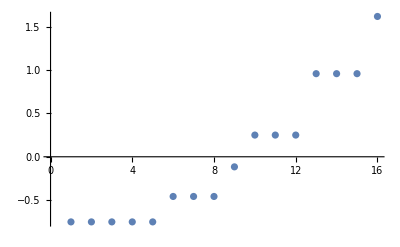

```mathematica
ListPlot[solA[[1]]+shift]
```

Module 4: Entanglement entropy for subsystem from a bi-partition
The algorithm for reduced density matrix and EE work for both pure and mixed states
Note: I use log with base 2 in defining EE. Therefore, EE_max = -N1(1/N1)Log[2, 2^N1] =N1 . Here, N1 is the no of spins in subsystem 1 (not necessarily A)
partition is the location of bi-partitioning the system, not necessarily the same as nA
Module partial trace out anything starting from (partition+1)

```mathematica
SA[Ψ_,partition_]:=(
l1=Table[2,2n];
l2=Table[{j,n+j},{j,partition+1,n}];
l3=Join[{Table[j,{j,1,partition}],Table[j+partition,{j,1,partition}]}];

Clear[ρ,ρA,rhoP,EEA];
ϵ=10^(-12); (* a small number to remove divergence in calculating von Neumann entropy *)

ρ=KroneckerProduct[Ψ,Conjugate[Ψ]];
rhoP=ArrayReshape[ρ,l1];
ρA=TensorContract[rhoP,l2];
ρA=Flatten[ρA,l3];
λ=Eigenvalues[ρA]//Chop;
EEA=-Sum[λ[[j]]*Log[2,λ[[j]]+ϵ],{j,1,2^partition}]//Chop;
Clear[l1,l2,l3];
);
```

```mathematica
(* Timing[
SAlist=Table[{},n-1];
Do[
Do[
SA[vec[[i]],j];
SAlist[[j]]=Append[SAlist[[j]],{en[[i]],EEA}];,
{i,1,dim}];,
{j,1,n-1}];
] *)

(* Only for half cut to save time *)
Timing[
SAlist={};

Do[
SA[vec[[i]],cut];
SAlist=Append[SAlist,{en[[i]],EEA}];,
{i,1,dim}];
]
```

{13.4927,Null}

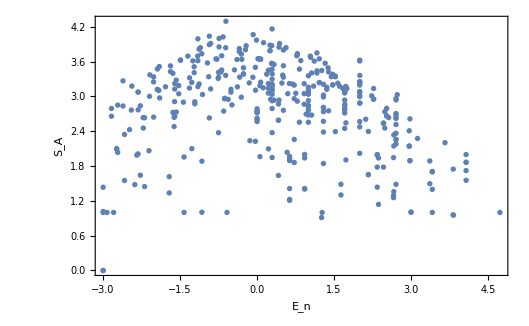

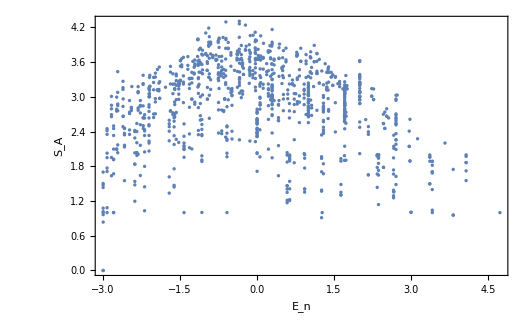

```mathematica
sector=0; (* Choose the Sx sector to plot EE *)
ListPlot[SAlist[[Sxclass[[sector+n/2+1]]]],PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}]
ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}]
```

```mathematica
Print["Spectrum for H: ",en]
```

Spectrum for H: {-4.04631,-3.46803,-3.36803,-3.32472,-3.26803,-3.22472,-3.16854,-3.12472,-3.06854,-3.0525,-3.00786,-2.96854,-2.9525,-2.90786,-2.8525,-2.80786,-2.78682,-2.68682,-2.64723,-2.58682,-2.56366,-2.54723,-2.53491,-2.50476,-2.49779,-2.48942,-2.48682,-2.46366,-2.44723,-2.43491,-2.40484,-2.39779,-2.38942,-2.38682,-2.3727,-2.36366,-2.34723,-2.33865,-2.33491,-2.32254,-2.30484,-2.29779,-2.28942,-2.2727,-2.2658,-2.26069,-2.24723,-2.23491,-2.22254,-2.22049,-2.20484,-2.19779,-2.18942,-2.1727,-2.16565,-2.16069,-2.13574,-2.13491,-2.12254,-2.12049,-2.11822,-2.11784,-2.09779,-2.08942,-2.0727,-2.06565,-2.06069,-2.02049,-2.01822,-2.01784,-2.01772,-2.00986,-1.99433,-1.9727,-1.96565,-1.96069,-1.95729,-1.91822,-1.91784,-1.91772,-1.90986,-1.89682,-1.86565,-1.86069,-1.85729,-1.85347,-1.84878,-1.81784,-1.81772,-1.80986,-1.79682,-1.77622,-1.76565,-1.75729,-1.75347,-1.73058,-1.72334,-1.71784,-1.71772,-1.70986,-1.70286,-1.69682,-1.68904,-1.68037,-1.67622,-1.66411,-1.65674,-1.65347,-1.64205,-1.63058,-1.62334,-1.61772,-1.61658,-1.60986,-1.60286,-1.60171,-1.59682,-1.58904,-1.58037,-1.57622,-1.57179,-1.56411,-1.55674,-1.55347,-1.54914,-1.54507,-1.54205,-1.53058,-1.52928,-1.52785,-1.52334,-1.51658,-1.51016,-1.50986,-1.50286,-1.50171,-1.49682,-1.48904,-1.48246,-1.48037,-1.47622,-1.47179,-1.47022,-1.46411,-1.45674,-1.45347,-1.44914,-1.44507,-1.44205,-1.43058,-1.42928,-1.42874,-1.41658,-1.41016,-1.40986,-1.40385,-1.40171,-1.40103,-1.39912,-1.39682,-1.38904,-1.38776,-1.38037,-1.37622,-1.37179,-1.37022,-1.35347,-1.35255,-1.34914,-1.34561,-1.34507,-1.33058,-1.32928,-1.31658,-1.31016,-1.30898,-1.30385,-1.30103,-1.29682,-1.28904,-1.28776,-1.28037,-1.27022,-1.25738,-1.25347,-1.25255,-1.24914,-1.24561,-1.24558,-1.24507,-1.23058,-1.22928,-1.21658,-1.21361,-1.20898,-1.20385,-1.20103,-1.18776,-1.18037,-1.17022,-1.16858,-1.16479,-1.15738,-1.15255,-1.15,-1.14914,-1.14561,-1.14507,-1.13058,-1.12928,-1.12458,-1.11361,-1.10898,-1.10793,-1.10106,-1.10103,-1.09144,-1.08776,-1.08037,-1.07022,-1.06858,-1.06479,-1.05738,-1.05,-1.04914,-1.04507,-1.04481,-1.02458,-1.01361,-1.00898,-1.00793,-1.00106,-1.00103,-0.991442,-0.987762,-0.968912,-0.968578,-0.964787,-0.959017,-0.957382,-0.95,-0.949141,-0.945075,-0.944811,-0.939612,-0.934499,-0.924585,-0.923374,-0.920718,-0.916699,-0.914573,-0.913612,-0.908981,-0.907932,-0.901057,-0.901028,-0.891442,-0.883553,-0.868912,-0.868578,-0.864787,-0.859017,-0.857382,-0.85,-0.849841,-0.844811,-0.839612,-0.834499,-0.824585,-0.823374,-0.822883,-0.820718,-0.816699,-0.814573,-0.813612,-0.8125,-0.808981,-0.807932,-0.801057,-0.801028,-0.795604,-0.783553,-0.783264,-0.782195,-0.7783,-0.774566,-0.769269,-0.768912,-0.768578,-0.764787,-0.763604,-0.759017,-0.755389,-0.75,-0.749841,-0.739612,-0.737785,-0.73564,-0.734499,-0.724585,-0.723678,-0.723374,-0.722883,-0.720718,-0.717423,-0.716699,-0.714573,-0.708981,-0.707932,-0.701057,-0.699893,-0.689314,-0.683553,-0.683264,-0.682195,-0.6783,-0.676921,-0.674566,-0.669269,-0.668912,-0.663604,-0.659017,-0.655389,-0.652202,-0.65,-0.649841,-0.647189,-0.639612,-0.637785,-0.63564,-0.624585,-0.623847,-0.623678,-0.622883,-0.620718,-0.617423,-0.614573,-0.607375,-0.601057,-0.598806,-0.593238,-0.584392,-0.583264,-0.582195,-0.5783,-0.576921,-0.574566,-0.569269,-0.568912,-0.56852,-0.563604,-0.559017,-0.555389,-0.552767,-0.552436,-0.552202,-0.55,-0.547189,-0.546255,-0.539612,-0.537785,-0.53564,-0.53266,-0.524585,-0.523847,-0.523678,-0.520718,-0.51819,-0.517423,-0.514573,-0.507375,-0.501057,-0.498806,-0.493238,-0.492072,-0.484392,-0.483264,-0.482195,-0.476921,-0.474566,-0.469269,-0.46852,-0.459017,-0.459017,-0.458846,-0.452767,-0.452436,-0.452202,-0.45,-0.447189,-0.437785,-0.43564,-0.43266,-0.427716,-0.423861,-0.423847,-0.41819,-0.417423,-0.41617,-0.414573,-0.407375,-0.401057,-0.398806,-0.393238,-0.392072,-0.384392,-0.383264,-0.382195,-0.376921,-0.374566,-0.369269,-0.36852,-0.359017,-0.359017,-0.352767,-0.352436,-0.35,-0.337785,-0.33564,-0.33266,-0.327716,-0.323847,-0.31819,-0.317423,-0.31617,-0.314573,-0.313482,-0.307375,-0.301057,-0.30002,-0.293238,-0.292072,-0.285896,-0.284392,-0.282195,-0.276921,-0.273211,-0.26852,-0.259017,-0.259017,-0.252436,-0.25,-0.237785,-0.227716,-0.223847,-0.21617,-0.213482,-0.207375,-0.20002,-0.193238,-0.186756,-0.185896,-0.184392,-0.18306,-0.182195,-0.173211,-0.16852,-0.159017,-0.159017,-0.152436,-0.15,-0.145137,-0.138965,-0.137785,-0.137307,-0.135372,-0.116261,-0.1158,-0.113482,-0.109269,-0.10002,-0.0934407,-0.0932383,-0.0867563,-0.0858961,-0.0830602,-0.0732115,-0.0685199,-0.059017,-0.0524364,-0.05,-0.0454119,-0.0451369,-0.0425963,-0.0389649,-0.0377853,-0.0373069,-0.0353722,-0.0234181,-0.0162613,-0.0158002,-0.0134819,-0.013438,-0.00926863,-0.0000199713,0.00655933,0.00676172,0.00886354,0.0132437,0.0141039,0.0151116,0.0155676,0.0169398,0.0195805,0.0197744,0.0267885,0.0308963,0.0313205,0.0314801,0.040983,0.0453842,0.0475636,0.05,0.0540492,0.0545881,0.0548631,0.0574037,0.0586222,0.0607969,0.0610351,0.0622147,0.0626931,0.0646278,0.0664155,0.070696,0.0765819,0.0779708,0.0837387,0.0841998,0.0865181,0.086562,0.0907314,0.09998,0.102582,0.106559,0.108864,0.113244,0.114104,0.115112,0.115568,0.116498,0.116603,0.11694,0.119774,0.126789,0.130896,0.13132,0.140983,0.145384,0.15,0.154588,0.154863,0.157404,0.158622,0.159017,0.160797,0.162693,0.166415,0.175169,0.176582,0.177971,0.183739,0.1842,0.186518,0.186562,0.188083,0.190731,0.19998,0.202582,0.203851,0.206559,0.208864,0.213244,0.215112,0.215568,0.21694,0.219774,0.221678,0.227245,0.229197,0.230896,0.23132,0.23631,0.239204,0.240983,0.244859,0.245384,0.25,0.254863,0.257404,0.258622,0.259017,0.260797,0.262693,0.266415,0.270075,0.275169,0.277971,0.283739,0.2842,0.286518,0.286562,0.288083,0.290731,0.29998,0.302582,0.303851,0.306559,0.313244,0.315112,0.315568,0.315601,0.319774,0.321678,0.324884,0.327245,0.329197,0.339204,0.340983,0.35,0.357404,0.358622,0.359017,0.362693,0.366415,0.366511,0.370075,0.375169,0.377971,0.386562,0.388083,0.390731,0.399525,0.401137,0.402582,0.403851,0.406559,0.413244,0.415112,0.415568,0.415601,0.415604,0.419774,0.421678,0.424884,0.427245,0.429197,0.437785,0.439204,0.45,0.458622,0.459017,0.462693,0.462976,0.466415,0.466511,0.469556,0.470075,0.475169,0.477784,0.477971,0.490731,0.491516,0.499525,0.501137,0.502582,0.506559,0.515601,0.519774,0.521678,0.524884,0.529197,0.537785,0.55,0.559017,0.562976,0.566511,0.569556,0.570075,0.575169,0.577784,0.577971,0.580561,0.586417,0.599525,0.601137,0.615601,0.619774,0.621678,0.629197,0.636841,0.637785,0.641541,0.65,0.654584,0.659017,0.659017,0.662976,0.668628,0.669556,0.670075,0.677784,0.677971,0.680561,0.680653,0.686417,0.699525,0.701137,0.715601,0.717192,0.736841,0.737785,0.741541,0.75,0.754584,0.756583,0.757979,0.759017,0.759017,0.762976,0.768628,0.769556,0.769925,0.770075,0.777784,0.780561,0.780653,0.786417,0.799525,0.801057,0.801137,0.815601,0.817192,0.828064,0.829934,0.836841,0.837785,0.841541,0.842091,0.849243,0.854584,0.856583,0.857979,0.859017,0.859017,0.862976,0.866574,0.866751,0.868628,0.869556,0.869925,0.870075,0.872991,0.877784,0.880653,0.882279,0.901057,0.915601,0.917192,0.917507,0.919532,0.928064,0.929934,0.932848,0.937785,0.944646,0.949243,0.953125,0.954584,0.956583,0.957979,0.959017,0.959017,0.964329,0.966024,0.966574,0.966751,0.968628,0.969925,0.972991,0.977784,0.980653,0.982279,0.987801,0.996385,1.00106,1.01719,1.01751,1.01953,1.02197,1.02383,1.02806,1.02993,1.0312,1.03285,1.03779,1.04465,1.04646,1.04921,1.04924,1.05313,1.05458,1.05798,1.05902,1.06657,1.06675,1.06863,1.06993,1.07299,1.07778,1.08065,1.08228,1.0878,1.09639,1.10106,1.11719,1.11751,1.11953,1.12383,1.12806,1.12934,1.12993,1.13044,1.13285,1.13779,1.14465,1.14646,1.14921,1.14924,1.15313,1.15458,1.15798,1.15902,1.16993,1.17299,1.1878,1.19117,1.19217,1.19639,1.20106,1.21965,1.22383,1.22806,1.22934,1.22993,1.23044,1.23779,1.24646,1.24921,1.24924,1.25458,1.25798,1.25902,1.2615,1.27299,1.29117,1.30106,1.31965,1.32383,1.32934,1.32993,1.33044,1.34646,1.34921,1.35751,1.35798,1.35902,1.3615,1.36808,1.39117,1.40106,1.41965,1.42034,1.42383,1.42993,1.44646,1.44921,1.45751,1.45902,1.4615,1.46611,1.46808,1.47725,1.4859,1.49117,1.50106,1.51965,1.52034,1.52383,1.55744,1.55751,1.5615,1.56808,1.57725,1.5859,1.59117,1.59332,1.59827,1.60106,1.61364,1.61368,1.61965,1.62034,1.62383,1.65481,1.65744,1.65751,1.6615,1.66978,1.67725,1.6859,1.69332,1.69641,1.69827,1.71364,1.71368,1.71373,1.71965,1.72034,1.7389,1.75441,1.75481,1.75744,1.75751,1.76978,1.774,1.77697,1.77725,1.78476,1.7859,1.79332,1.79513,1.79641,1.79827,1.81314,1.81364,1.81368,1.81373,1.81965,1.82034,1.85441,1.85481,1.85744,1.86978,1.874,1.87552,1.87697,1.87725,1.8859,1.89332,1.89641,1.89827,1.91314,1.91373,1.92034,1.95441,1.95744,1.974,1.97552,1.97599,1.97697,1.9859,1.99332,1.99641,1.99827,2.01314,2.02034,2.05441,2.074,2.07552,2.0859,2.09332,2.09641,2.11314,2.14233,2.15441,2.174,2.19332,2.21314,2.24233,2.24517,2.24741,2.25441,2.25502,2.34233,2.34517,2.34741,2.35441,2.35502,2.40309,2.44233,2.44517,2.44741,2.45502,2.45861,2.48156,2.52576,2.54233,2.54517,2.55861,2.58156,2.60385,2.62576,2.64517,2.65861,2.66669,2.68156,2.69119,2.70385,2.72576,2.73704,2.76669,2.78156,2.79119,2.80385,2.86669,2.88156,2.89119,2.90385,3.00385,3.36536,3.45987,3.46536,3.56536}

Module 5: von Neumann entropy of each site - Partial tracing out all other spins
Note: I use log with base 2 in defining entropy, so the thermal value is Log(2,2)=1, but not ln 2

```mathematica
vN[Ψ_,k_]:=(
b1=Table[2,2n];
b2=Join[Table[{j,n+j},{j,1,k-1}],Table[{j,n+j},{j,k+1,n}]];

Clear[λ,ρ,ρk,rhoP,vNEE];
ϵ=10^(-12); (* a small number to remove divergence in calculating von Neumann entropy *)

ρ=KroneckerProduct[Ψ,Conjugate[Ψ]];
rhoP=ArrayReshape[ρ,b1];
ρk=TensorContract[rhoP,b2];
ρk=Flatten[ρk,{{1},{2}}];
λ=Eigenvalues[ρk]//Chop;
vnEE=-Sum[λ[[j]]*Log[2,λ[[j]]+ϵ],{j,1,2}]//Chop;
Clear[b1,b2]
);
```

Calculate physical quantities
Running time: 10 sites, 500 time steps, run time is about 5 mins
Running time: 12 sites, 250 time steps, run time is about 30 mins

```mathematica
Timing[
end=1000;

comp=Table[Conjugate[vec[[i]]].ψ//Chop,{i,1,dim}]; (* Calculate the components *)
Ψ[t_]:=Sum[Exp[-ⅈ*en[[j]]*t]*comp[[j]]*vec[[j]],{j,1,dim}];

Llist={}; (* Loschmidt echo *)
σxlist={}; (* Storing <Sz> at every site *)
σylist={}; (* Storing <Sz> at every site *)
σzlist={}; (* Storing <Sz> at every site *)
vNlist={}; (* Storing vN entropy at every site *)
corlist={}; (* Storing the correlation for the bond *)

HAlist={}; (* Storing <HA> *)
HBlist={}; (* Storing <HB> *)
EEAlist={}; (* Storing EE at half cut *)

(* For left subsystem *)
HL=HA[Ja]-Jab*((S[cut-1,1].S[cut,1]+S[cut-1,2].S[cut,2]+S[cut-1,3].S[cut,3])+
+(S[cut-1,1].S[cut+1,1]+S[cut-1,2].S[cut+1,2]+S[cut-1,3].S[cut+1,3])+(S[cut,1].S[cut+1,1]+S[cut,2].S[cut+1,2]+S[cut,3].S[cut+1,3]));

(* For right subsystem *)
HR=HB[Jb]-Jab*((S[cut,1].S[cut+1,1]+S[cut,2].S[cut+1,2]+S[cut,3].S[cut+1,3])+(S[cut,1].S[cut+2,1]+S[cut,2].S[cut+2,2]+S[cut,3].S[cut+2,3])+(S[cut+1,1].S[cut+2,1]+S[cut+1,2].S[cut+2,2]+S[cut+1,3].S[cut+2,3]));

Do[
Clear[wav, EEA,vnEE];
wav=Ψ[t];

(* Llist=Append[Llist,{t,Abs[Conjugate[ψ].wav]^2}]; *)

Do[
(* σxlist=Append[σxlist,Conjugate[wav].S[k,1].wav//Chop];
σylist=Append[σylist,Conjugate[wav].S[k,2].wav//Chop]; *)

σzlist=Append[σzlist,Conjugate[wav].S[k,3].wav//Chop];
vN[wav,k];
vNlist=Append[vNlist,vnEE]
,{k,1,n}];

HAlist=Append[HAlist,{t,Conjugate[wav].HL.wav//Chop}];
HBlist=Append[HBlist,{t,Conjugate[wav].HR.wav//Chop}];

(*
corlist=Append[corlist,{t,Conjugate[wav].(S[cut,1].S[cut+1,1]+S[cut,2].S[cut+1,2]+S[cut,3].S[cut+1,3]).wav}];
*)

SA[wav,cut]; 
EEAlist=Append[EEAlist,{t,EEA}];

,{t,0,end,end/250}];

(* σxlist=Partition[σxlist,n];
σylist=Partition[σylist,n]; *)

σzlist=Partition[σzlist,n];
vNlist=Partition[vNlist,n];
]
```

{1825.49,Null}

Heisenberg model with JA=JB=1, JAB=1
A start at |uuuu>, bond starts at a singlet state, and B starts at a random state

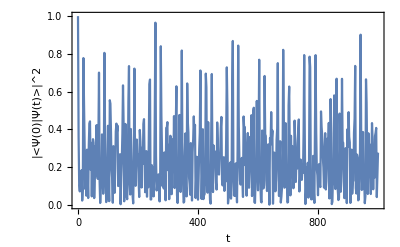

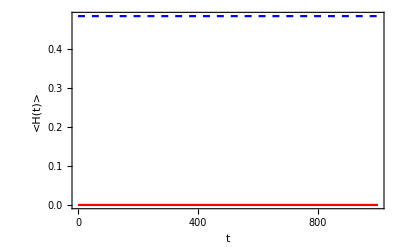

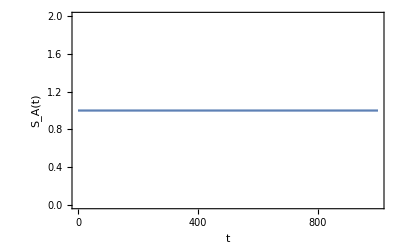

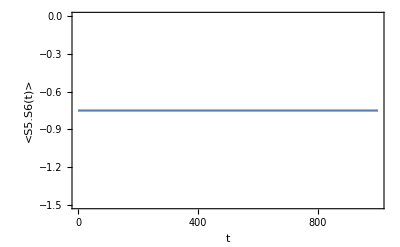

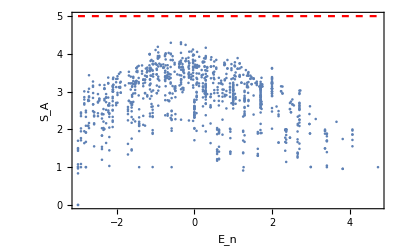

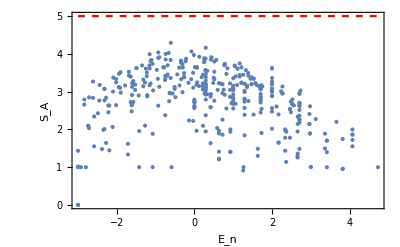

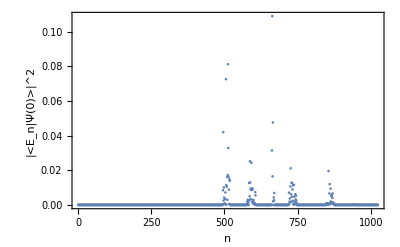

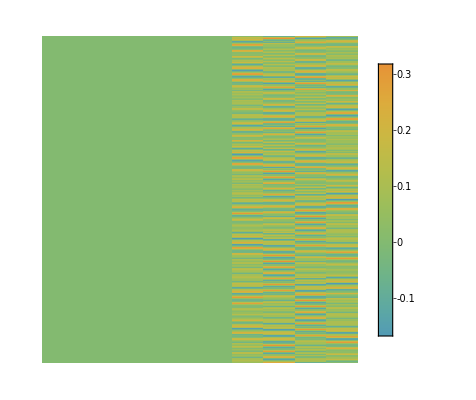

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[corlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","<S5.S6(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
Show[ListPlot[SAlist[[Sxclass[[sector+n/2+1]]]],PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σxlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σylist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```

Heisenberg model with JA=JB=1, JAB=1
A start at |uuuu>, bond starts at a random state, and B starts at a random state

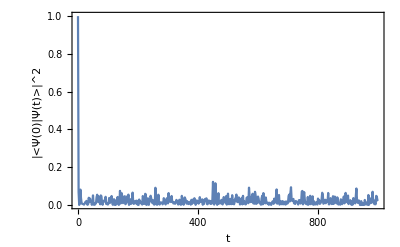

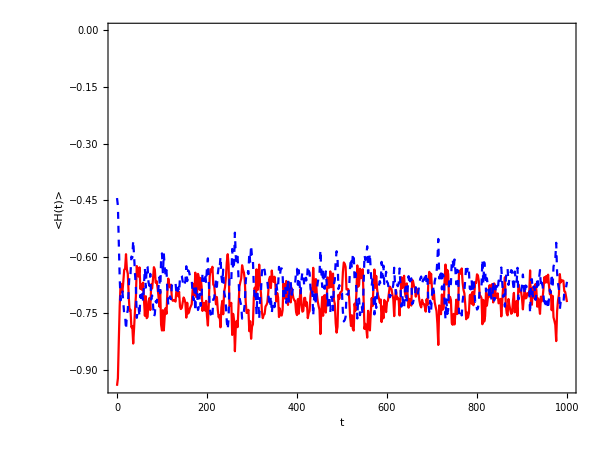

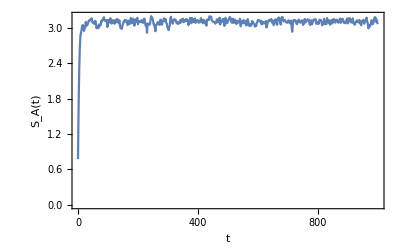

-Graphics-

-Graphics-

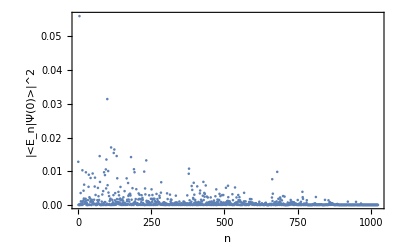

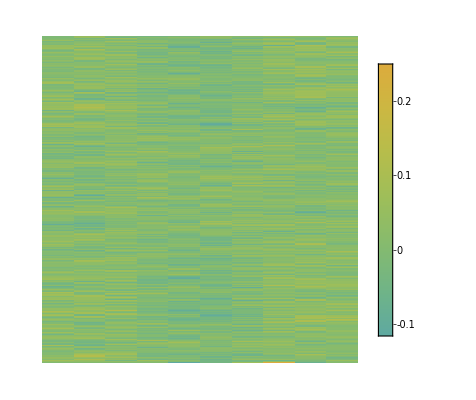

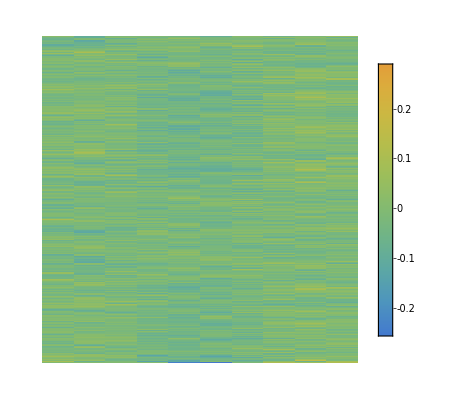

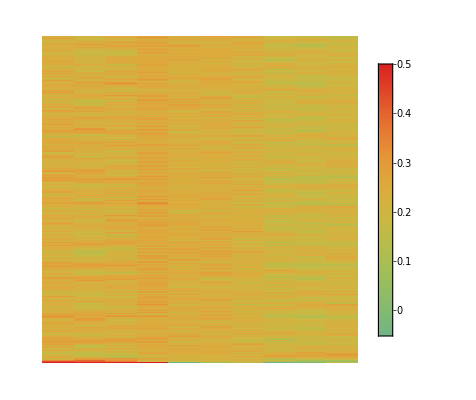

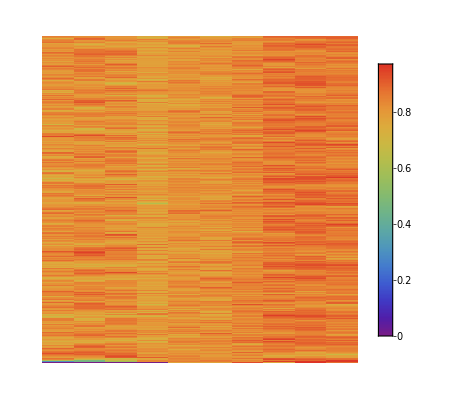

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
Show[ListPlot[SAlist[[Sxclass[[sector+n/2+1]]]],PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σxlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σylist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```

Heisenberg model with JA=JB=1, JAB=1
A start at |uuuu>, bond starts at (|ud>+|du>)/Sqrt[2], and B starts at a random state

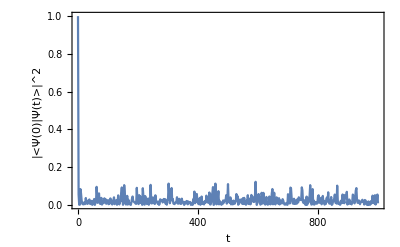

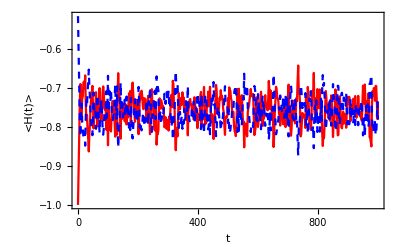

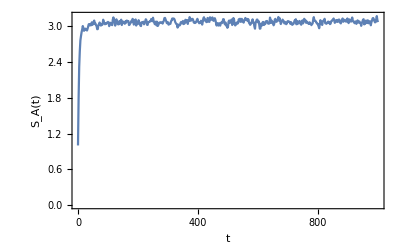

-Graphics-

-Graphics-

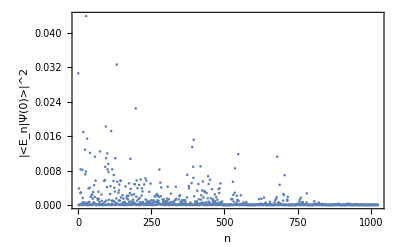

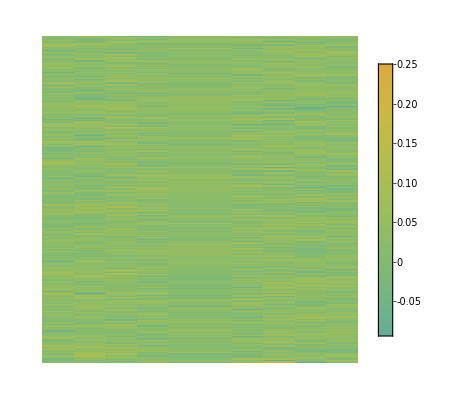

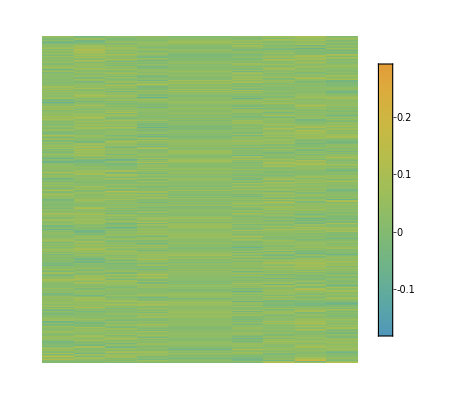

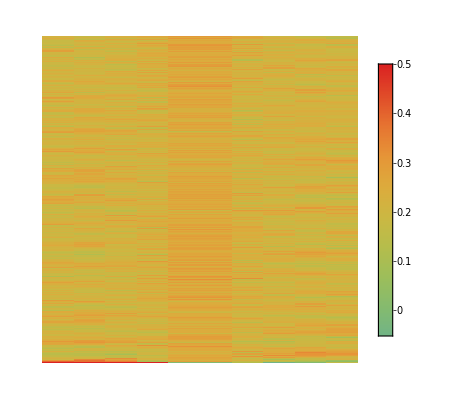

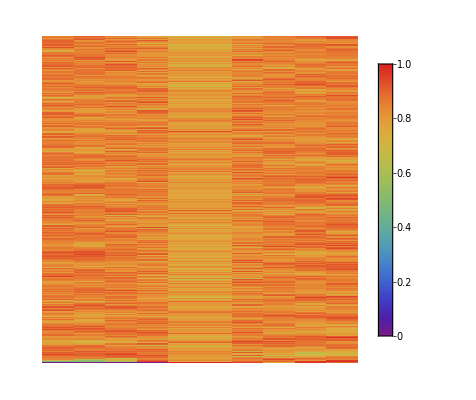

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
Show[ListPlot[SAlist[[Sxclass[[sector+n/2+1]]]],PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σxlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σylist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```

Heisenberg model with JA=JB=1, JAB=1
A start at |uuuu>, bond starts at (|ud>+|du>)/Sqrt[2], and B starts at a random state
Run to shorter time

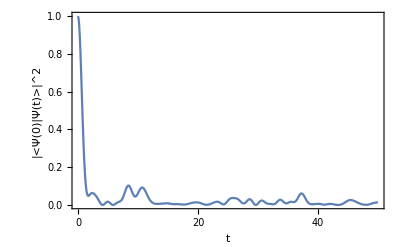

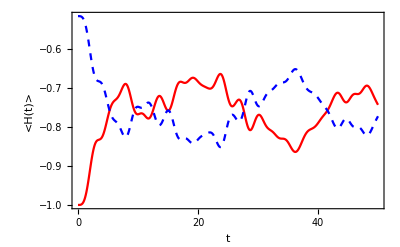

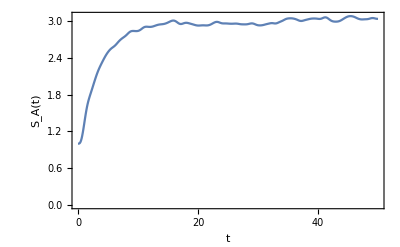

-Graphics-

-Graphics-

-Graphics-

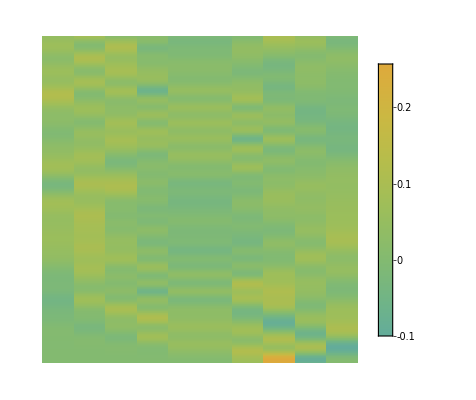

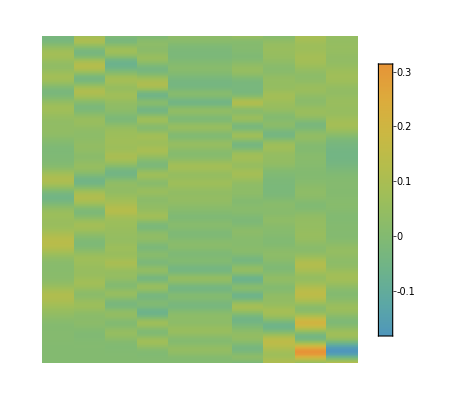

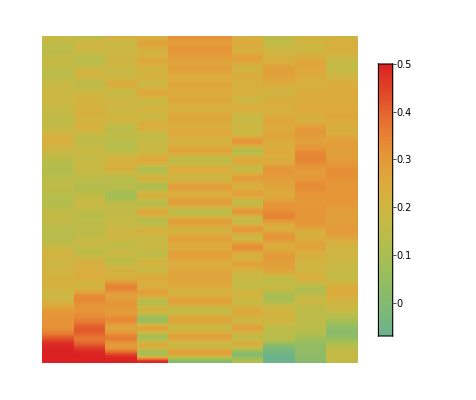

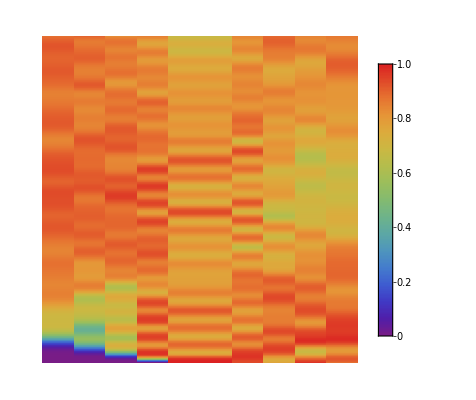

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

Show[ListPlot[SAlist,PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},RotateLabel->False],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
Show[ListPlot[SAlist[[Sxclass[[sector+n/2+1]]]],PlotRange->All,Frame->True,FrameLabel->{"E_n","S_A"},AxesOrigin->{0,0}],Plot[cut,{x,Min[en],Max[en]},PlotStyle->{Red,Dashed}],PlotRange->All]
ListPlot[Abs[comp]^2,PlotRange->All,Frame->True,FrameLabel->{"n","|<E_n|Ψ(0)>|^2"},RotateLabel->False]

ArrayPlot[σxlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σylist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```

Heisenberg model with JA=JB=1, JAB=1
12 spins
A start at |uuuuu>, bond starts at (|ud>+|du>)/Sqrt[2], and B starts at a random state

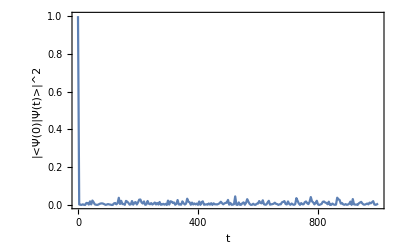

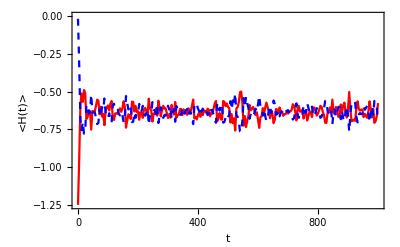

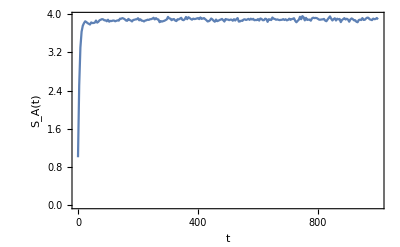

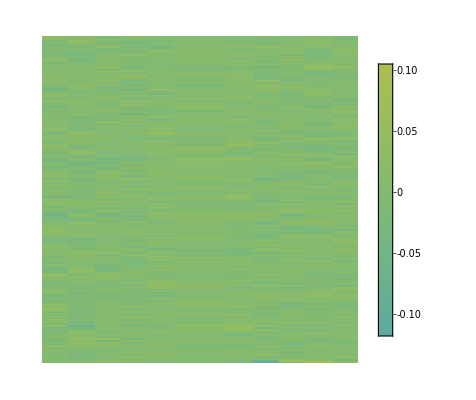

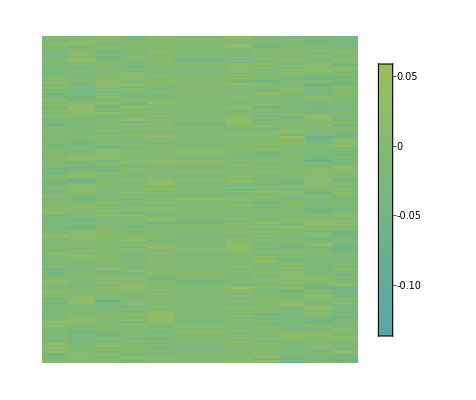

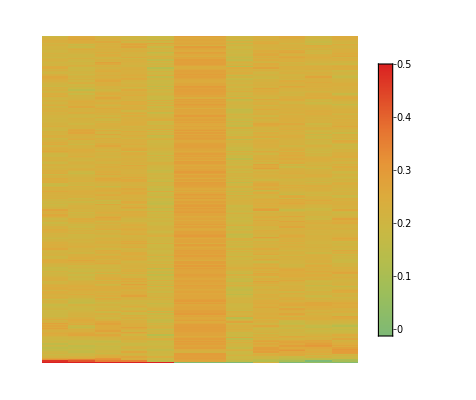

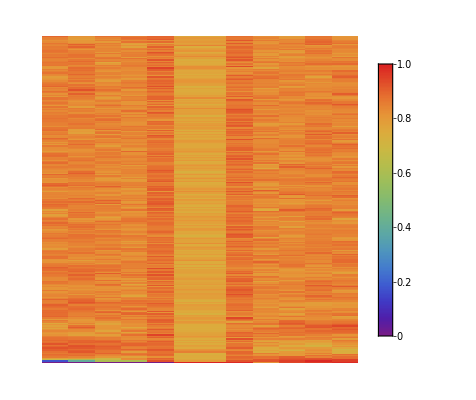

```mathematica
ListPlot[Llist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","|<Ψ(0)|Ψ(t)>|^2"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]
ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

ArrayPlot[σxlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σylist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```

Heisenberg model with JA=JB=1, JAB=1
12 spins
A start at |uuuuu>, bond starts at (|ud>-|du>)/Sqrt[2], and B starts at a random state

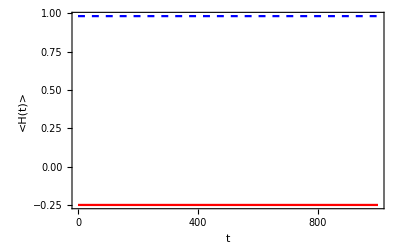

-Graphics-

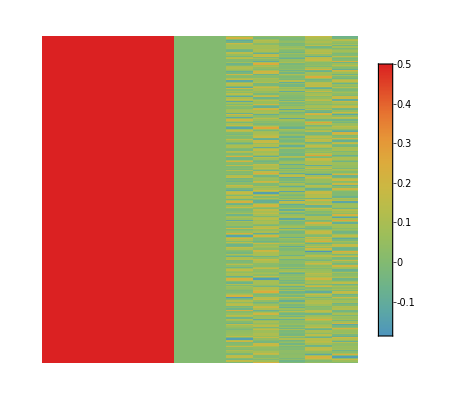

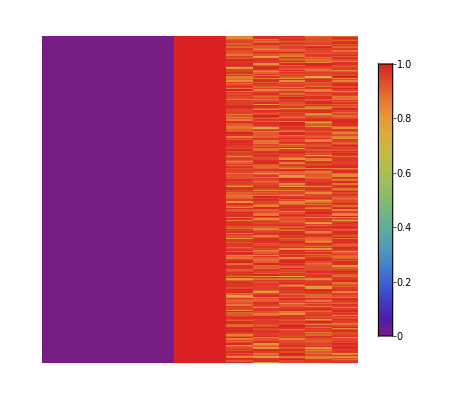

```mathematica
ListPlot[{HAlist,HBlist},PlotRange->All,Joined->True,PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{"t","<H(t)>"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

ListPlot[EEAlist,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","S_A(t)"},RotateLabel->False,FrameTicks->{{0,end/5,2end/5,3end/5,4end/5,end},Automatic}]

ArrayPlot[σzlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-0.5,0.5}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]

ArrayPlot[vNlist,PlotRange->All,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->All,PlotLegends->Automatic,AspectRatio->1,DataReversed->{True,False},FrameLabel->{"t","j"}]
```